# Region plots

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";
(*directory to save figures in*)
```

## Life-cycle

### Haploid competition

Frequency of haploids from each sex

```mathematica
Subscript[freqHap, sex_]:=ParallelSum[Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}]
```

Mean haploid fitness of gametes from each sex

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}]/Subscript[freqHap, sex]
```

Frequencies of haploid genotypes from each sex following haploid competition, which occurs between gametes coming from the same sex

```mathematica
Subscript[fHapSel, x_,y_,z_,sex_]:=(Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex])/(Subscript[wbarHap, sex] Subscript[freqHap, sex])
```

### Random mating

Gametes from the two sexes pair at random

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

### Sex determination

Determine the sex of newly formed diploids

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

Rules for invasion of a dominant modifier into an XY system (relabeling males and females and females as males, as well as Y as W and X as Z makes the ancestral system ZW)

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if neo-SD allele wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female neo-SD allele wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the maternal neo-SD locus*)
Subscript[psex, zM_,xP_,m,female]->k (*female with probability k if mutation at the paternal neo-SD locus*)
};
```

### Diploid selection

Frequencies of diploids from each sex

```mathematica
Subscript[freqDip, sex_]:=ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Mean diploid fitness in each sex

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]/Subscript[freqDip, sex]
```

Frequencies of diploid genotypes in each sex following diploid selection, which occurs separately in each sex (even if diploid selection is not direct competition between members of the same sex but instead viability selection, selection still effectively occurs ‘separately in each sex’ because the next generation is sired by 50% males and 50% females)

```mathematica
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=(Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex])/(Subscript[wbarDip, sex] Subscript[freqDip, sex])
```

### Meiosis

Gamete genotypes produced by diploids

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

#### Segregation

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, male])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(recAXnotAM+recAMnotAX)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(recAXnotAM+recAMnotAX)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->Subscript[α, male] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->Subscript[α, male] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->Subscript[α, male] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-Subscript[α, male]) recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z1_]->Subscript[α, female] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z2_]->Subscript[α, female] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z1_]->Subscript[α, female] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z2_]->(1-Subscript[α, female]) recAXandAM
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

#### Recombination probabilities for different arrangements of loci

Let the probability of recombination (an odd number of cross-overs) between loci A and X be r, the probability of recombination between A and M be R, and the probability of recombination between X and M be χ.

We can then write, in general,

```mathematica
recGen={
recAXnotAM->(r+χ-R)/2,
recAMnotAX->(R+χ-r)/2,
recAXandAM->(r+R-χ)/2
};
```

and for specific orders of loci we can substitute in the value of χ (alternatively one could do the same for R or r)

```mathematica
χAXM=χ->R(1-r)+r(1-R);
χXAM=χ->(r-R)/(1-2R);
χXMA=χ->(R-r)/(1-2r);
```

## Resident equilibrium (tight linkage between X and A; r=0)

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following four equations are zero

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume tight linkage between A and X

```mathematica
weakrecAX={
recAXandAM->recAXandAM ϵ,
recAXnotAM->recAXnotAM ϵ
};
```

Without recombination the recursions for the change in the frequencies are

```mathematica
differenceEqsr0=Normal[Series[differenceEqs/.weakrecAX,{ϵ,0,0}]]//Simplify
```

{(-(-1+pXf) wHap_(a,female) (pXf (-1+pXm) wHap_(a,male) wDip_(a,a,female)+pXm (-pXf+α_female) wHap_(A,male) wDip_(a,A,female))+pXf wHap_(A,female) ((-1+pXm) (pXf-α_female) wHap_(a,male) wDip_(A,a,female)-(-1+pXf) pXm wHap_(A,male) wDip_(A,A,female)))/((-1+pXf) wHap_(a,female) ((-1+pXm) wHap_(a,male) wDip_(a,a,female)-pXm wHap_(A,male) wDip_(a,A,female))+pXf wHap_(A,female) (-(-1+pXm) wHap_(a,male) wDip_(A,a,female)+pXm wHap_(A,male) wDip_(A,A,female))),(2 (-1+freqYm) (-1+pXf) pXm wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-2 (-1+pYm) ((-1+freqYm) pXm+α_male) wHap_(a,male) wDip_(A,a,male)+(1+2 (-1+freqYm) pXm) pYm wHap_(A,male) wDip_(A,A,male)))/(2 ((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-(-1+pYm) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male)))),(pYm (-2 (-1+pXf) wHap_(a,female) (freqYm (-1+pYm) wHap_(a,male) wDip_(a,a,male)+(-freqYm pYm+α_male) wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (2 freqYm (-1+pYm) wHap_(a,male) wDip_(A,a,male)+(1-2 freqYm pYm) wHap_(A,male) wDip_(A,A,male))))/(2 ((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-(-1+pYm) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male)))),(-(-1+pXf) wHap_(a,female) ((-1+2 freqYm) (-1+pYm) wHap_(a,male) wDip_(a,a,male)+2 pYm (-freqYm+α_male) wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (2 (-1+pYm) (-1+freqYm+α_male) wHap_(a,male) wDip_(A,a,male)+(1-2 freqYm) pYm wHap_(A,male) wDip_(A,A,male)))/(2 ((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-(-1+pYm) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male))))}

To help Mathematica, we solve for each in turn.

The frequency of Ys from males at equilbirum is

```mathematica
solfreqYmr0=Solve[0==differenceEqsr0[[4]],freqYm]//Simplify//Flatten
```

{freqYm→((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-2 pYm α_male wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (2 (-1+pYm) (-1+α_male) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male)))/(2 ((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-(-1+pYm) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male))))}

We can use this to solve for the frequency of A on Ys from males

```mathematica
solpYmr0a=Solve[0==differenceEqsr0[[3]]/.solfreqYmr0,pYm][[1]]//Simplify
solpYmr0A=Solve[0==differenceEqsr0[[3]]/.solfreqYmr0,pYm][[2]]//Simplify
```

{pYm→0}

{pYm→1}

Thus the Y is fixed for either a or A.

When a is fixed on the Y the frequencies on the Xs are

```mathematica
Solve[0==differenceEqsr0[[2]]/.solfreqYmr0/.solpYmr0a,pXm]//Simplify//Flatten;
solpXfr0a=Solve[0==differenceEqsr0[[1]]/.solfreqYmr0/.solpYmr0a/.%,pXf]//Simplify
solpXmr0a=%%/.%//Simplify
```

{{pXf→0},{pXf→1},{pXf→(wHap_(a,female) (wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-wHap_(a,female) wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+2 α_male wHap_(A,female)^2 wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female))}}

{{pXm→0},{pXm→1},{pXm→(2 α_male wDip_(A,a,male) (-wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)+α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female) wDip_(a,a,male) (-2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) (-(-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 α_male wDip_(a,a,female) wDip_(A,a,male)))+2 α_male wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female)))}}

So when a is fixed in the population we have

```mathematica
eqr0YaXa={solpYmr0a,solpXfr0a[[1]],solpXmr0a[[1]],solfreqYmr0/.solpYmr0a/.solpXfr0a[[1]]}//Simplify//Flatten
```

{pYm→0,pXf→0,pXm→0,freqYm→1/2}

when a is fixed on the Y and A is fixed on the X we have

```mathematica
eqr0YaXA={solpYmr0a,solpXfr0a[[2]],solpXmr0a[[2]],solfreqYmr0/.solpYmr0a/.solpXfr0a[[2]]}//Simplify//Flatten
```

{pYm→0,pXf→1,pXm→1,freqYm→1-α_male}

and when a is fixed on the Y and the X is polymorphic we have

```mathematica
eqr0YaXAa={solpYmr0a,solpXfr0a[[3]],solpXmr0a[[3]],solfreqYmr0/.solpYmr0a/.solpXfr0a[[3]]}//Simplify//Flatten
```

{pYm→0,pXf→(wHap_(a,female) (wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-wHap_(a,female) wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+2 α_male wHap_(A,female)^2 wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female)),pXm→(2 α_male wDip_(A,a,male) (-wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)+α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female) wDip_(a,a,male) (-2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) (-(-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 α_male wDip_(a,a,female) wDip_(A,a,male)))+2 α_male wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female))),freqYm→(wHap_(a,female) wDip_(a,a,male) (2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) ((-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 (-1+α_male) wDip_(a,a,female) wDip_(A,a,male)))+2 wHap_(A,female) wDip_(A,a,male) (α_female (-1+α_male) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+α_male wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female)))/(2 (wHap_(a,female) wDip_(a,a,male) (2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) ((-1+α_female) wDip_(a,a,male) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,a,male)))-wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-2 α_male wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female))))}

When A is fixed on the Y the frequencies on the Xs are

```mathematica
Solve[0==differenceEqsr0[[2]]/.solfreqYmr0/.solpYmr0A,pXm]//Simplify//Flatten;
solpXfr0A=Solve[0==differenceEqsr0[[1]]/.solfreqYmr0/.solpYmr0A/.%,pXf]//Simplify
solpXmr0A=%%/.%//Simplify
```

{{pXf→0},{pXf→1},{pXf→(wHap_(a,female) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)-wHap_(A,female)^2 wHap_(A,male) wDip_(A,A,female) wDip_(A,A,male)+wHap_(a,female) wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))}}

{{pXm→0},{pXm→1},{pXm→(wDip_(A,A,male) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(-2 (-1+α_male) wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) (-1+α_male) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (2 (-1+α_male) wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))}}

So when A is fixed in the population we have

```mathematica
eqr0YAXA={solpYmr0A,solpXfr0A[[2]],solpXmr0A[[2]],solfreqYmr0/.solpYmr0A/.solpXfr0A[[2]]}//Simplify//Flatten
```

{pYm→1,pXf→1,pXm→1,freqYm→1/2}

when A is fixed on the Y and a is fixed on the X we have

```mathematica
eqr0YAXa={solpYmr0A,solpXfr0A[[1]],solpXmr0A[[1]],solfreqYmr0/.solpYmr0A/.solpXfr0A[[1]]}//Simplify//Flatten
```

{pYm→1,pXf→0,pXm→0,freqYm→α_male}

and when A is fixed on the Y and the X is polymorphic we have

```mathematica
eqr0YAXAa={solpYmr0A,solpXfr0A[[3]],solpXmr0A[[3]],solfreqYmr0/.solpYmr0A/.solpXfr0A[[3]]}//Simplify//Flatten
```

{pYm→1,pXf→(wHap_(a,female) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)-wHap_(A,female)^2 wHap_(A,male) wDip_(A,A,female) wDip_(A,A,male)+wHap_(a,female) wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))),pXm→(wDip_(A,A,male) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(-2 (-1+α_male) wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) (-1+α_male) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (2 (-1+α_male) wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))),freqYm→(4 (-1+α_female) α_male^2 wHap_(a,female) wHap_(a,male) wDip_(a,A,male)^2 wDip_(A,a,female)+wDip_(A,A,male) (-2 wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (2 wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))-2 α_male wDip_(a,A,male) (wHap_(A,female) (α_female wHap_(a,male) wDip_(A,a,female)+wHap_(A,male) wDip_(A,A,female)) wDip_(A,A,male)+wHap_(a,female) ((-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))))/(2 (wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+2 (-1+α_male) wHap_(a,male) ((-1+α_female) wDip_(a,A,male) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (-wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))))}

Thus we have derived 6 resident equilibria with absolutely no recombination between A and M and we next see which are stable.

```mathematica
eqr0YAXA
eqr0YAXAa
eqr0YAXa
eqr0YaXA
eqr0YaXAa
eqr0YaXa
```

{pYm→1,pXf→1,pXm→1,freqYm→1/2}

{pYm→1,pXf→(wHap_(a,female) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)-wHap_(A,female)^2 wHap_(A,male) wDip_(A,A,female) wDip_(A,A,male)+wHap_(a,female) wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))),pXm→(wDip_(A,A,male) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(-2 (-1+α_male) wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) (-1+α_male) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (2 (-1+α_male) wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))),freqYm→(4 (-1+α_female) α_male^2 wHap_(a,female) wHap_(a,male) wDip_(a,A,male)^2 wDip_(A,a,female)+wDip_(A,A,male) (-2 wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (2 wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))-2 α_male wDip_(a,A,male) (wHap_(A,female) (α_female wHap_(a,male) wDip_(A,a,female)+wHap_(A,male) wDip_(A,A,female)) wDip_(A,A,male)+wHap_(a,female) ((-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))))/(2 (wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+2 (-1+α_male) wHap_(a,male) ((-1+α_female) wDip_(a,A,male) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (-wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))))}

{pYm→1,pXf→0,pXm→0,freqYm→α_male}

{pYm→0,pXf→1,pXm→1,freqYm→1-α_male}

{pYm→0,pXf→(wHap_(a,female) (wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-wHap_(a,female) wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+2 α_male wHap_(A,female)^2 wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female)),pXm→(2 α_male wDip_(A,a,male) (-wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)+α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female) wDip_(a,a,male) (-2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) (-(-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 α_male wDip_(a,a,female) wDip_(A,a,male)))+2 α_male wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female))),freqYm→(wHap_(a,female) wDip_(a,a,male) (2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) ((-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 (-1+α_male) wDip_(a,a,female) wDip_(A,a,male)))+2 wHap_(A,female) wDip_(A,a,male) (α_female (-1+α_male) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+α_male wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female)))/(2 (wHap_(a,female) wDip_(a,a,male) (2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) ((-1+α_female) wDip_(a,a,male) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,a,male)))-wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-2 α_male wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female))))}

{pYm→0,pXf→0,pXm→0,freqYm→1/2}

## Resident stability (tight linkage between X and A; r=0)

### General

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female]],
D[eqs,Subscript[fHap, X,a,M,female]],
D[eqs,Subscript[fHap, X,A,M,male]],
D[eqs,Subscript[fHap, X,a,M,male]],
D[eqs,Subscript[fHap, Y,A,M,male]],
D[eqs,Subscript[fHap, Y,a,M,male]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial;

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Some useful assumptions

```mathematica
posassumps={Table[0<Subscript[α, sex]<1,{sex,{male,female}}],Table[Subscript[wDip, x,y,sex]>0,{x,{A,a}},{y,{A,a}},{sex,{male,female}}],,Table[Subscript[wHap, y,sex]>0,{y,{A,a}},{sex,{male,female}}]}//Flatten;
```

### Equilibrium YA XA (blue)

```mathematica
YAXAEigs=Simplify[Solve[0==Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YAXA,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→-(2 (-1+α_male) wHap_(a,male) wDip_(A,a,male))/(wHap_(A,male) wDip_(A,A,male))},{λ→(-(-1+α_female) wHap_(a,female) wDip_(a,A,female) √(wHap_(A,male) wDip_(A,A,male))-√((-1+α_female) wHap_(a,female)) √(8 (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female) wDip_(A,A,female)+(-1+α_female) wHap_(a,female) wHap_(A,male) wDip_(a,A,female)^2 wDip_(A,A,male)))/(2 wHap_(A,female) wDip_(A,A,female) √(wHap_(A,male) wDip_(A,A,male)))},{λ→(-(-1+α_female) wHap_(a,female) wDip_(a,A,female) √(wHap_(A,male) wDip_(A,A,male))+√((-1+α_female) wHap_(a,female)) √(8 (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female) wDip_(A,A,female)+(-1+α_female) wHap_(a,female) wHap_(A,male) wDip_(a,A,female)^2 wDip_(A,A,male)))/(2 wHap_(A,female) wDip_(A,A,female) √(wHap_(A,male) wDip_(A,A,male)))}}

### Equilibrium Ya Xa (red)

```mathematica
YaXaEigs=Simplify[Solve[0==Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YaXa,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→(2 α_male wHap_(A,male) wDip_(a,A,male))/(wHap_(a,male) wDip_(a,a,male))},{λ→(α_female wHap_(A,female) wDip_(A,a,female)-√(α_female wHap_(A,female) (α_female wHap_(A,female) wDip_(A,a,female)^2+(8 α_male wHap_(a,female) wHap_(A,male) wDip_(a,a,female) wDip_(a,A,female) wDip_(A,a,male))/(wHap_(a,male) wDip_(a,a,male)))))/(2 wHap_(a,female) wDip_(a,a,female))},{λ→(α_female wHap_(A,female) wDip_(A,a,female)+√(α_female wHap_(A,female) (α_female wHap_(A,female) wDip_(A,a,female)^2+(8 α_male wHap_(a,female) wHap_(A,male) wDip_(a,a,female) wDip_(a,A,female) wDip_(A,a,male))/(wHap_(a,male) wDip_(a,a,male)))))/(2 wHap_(a,female) wDip_(a,a,female))}}

### Equilibrium YA Xa (green)

```mathematica
YAXaEigs=Simplify[Solve[0==Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YAXa,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→(wHap_(a,male) wDip_(a,a,male))/(2 α_male wHap_(A,male) wDip_(a,A,male))},{λ→(α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female)-√(α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) (α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female)^2-2 wHap_(a,female) wHap_(A,male) wDip_(a,a,female) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male))},{λ→(α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female)+√(α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) (α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female)^2-2 wHap_(a,female) wHap_(A,male) wDip_(a,a,female) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male))}}

### Equilibrium Ya XA (puple)

```mathematica
YaXAEigs=Simplify[Solve[0==Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YaXA,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→-((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+√((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(A,a,male) ((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)^2 wDip_(A,a,male)-2 wHap_(a,male) wHap_(A,female) wDip_(a,a,male) wDip_(A,a,female) wDip_(A,A,female))))/(2 α_male wHap_(A,female) wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female))},{λ→(-(-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+√((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(A,a,male) ((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)^2 wDip_(A,a,male)-2 wHap_(a,male) wHap_(A,female) wDip_(a,a,male) wDip_(A,a,female) wDip_(A,A,female))))/(2 α_male wHap_(A,female) wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female))},{λ→-(wHap_(A,male) wDip_(A,A,male))/(2 (-1+α_male) wHap_(a,male) wDip_(A,a,male))}}

### Equilibrium Ya XAa (brown)

```mathematica
charpolyYaXAar0=Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YaXAa,{ϵ,0,0}]];
```

### Equilibrium YA XAa (yellow)

```mathematica
charpolyYAXAar0=Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YAXAa,{ϵ,0,0}]];
```

### Resident stability plot (no haploid selection, no sex differences)

#### Parameters

```mathematica
params={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,sex_]->Subscript[wDip, a,a],Subscript[wDip, A,A,sex_]->Subscript[wDip, A,A]
};
YAXAstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.params//Flatten]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXastabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.params//Flatten]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXastabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.params//Flatten]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.params//Flatten]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.params,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAastabplot=RegionPlot[
Max[Abs[intYaXAar0]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.params,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAastabplot=RegionPlot[
Max[Abs[intYAXAar0]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
YAXAstabplot,YaXastabplot,YAXastabplot,YaXAstabplot,YAXAastabplot,YaXAastabplot,
Epilog->{
Text["YA XAa stable",{1.6,0.9}],
Text["YA XAa stable",{0.5,0.75}],
Text["Ya XAa stable",{0.75,0.5}],
Rotate[Text["Ya XAa stable",{0.9,1.5}],π/2],
Text["Ya XA stable",{0.25,0.9}],
Text["YA Xa stable",{0.8,0.15}],
Rotate[Text["Ya Xa stable",{1.1,0.9}],π/2],
Text["YA XA stable",{0.9,1.1}]
},
PlotRangePadding->None,
FrameLabel->{"W_aa","W_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0"
]
```

-Graphics-

## Invasion (tight linkage between X and A; r=0)

### General

Jacobian for the mutants

```mathematica
eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
matExtFull=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
```

Characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

### Equilibrium YA XA

```mathematica
YAXAExtEigs=Simplify[Solve[0==Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YAXA,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→1},{λ→1-recAMnotAX},{λ→(2 (-1+recAMnotAX) (-1+α_female) wHap_(a,female) wDip_(a,A,female))/(wHap_(A,female) wDip_(A,A,female))},{λ→(2 (-1+recAMnotAX) (-1+α_female) wHap_(a,female) wDip_(a,A,female))/(wHap_(A,female) wDip_(A,A,female))}}

### Equilibrium Ya Xa

```mathematica
YaXaExtEigs=Simplify[Solve[0==Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YaXa,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→1},{λ→1-recAMnotAX},{λ→-(2 (-1+recAMnotAX) α_female wHap_(A,female) wDip_(A,a,female))/(wHap_(a,female) wDip_(a,a,female))},{λ→-(2 (-1+recAMnotAX) α_female wHap_(A,female) wDip_(A,a,female))/(wHap_(a,female) wDip_(a,a,female))}}

### Equilibrium YA Xa

```mathematica
YAXaExtEigs=Simplify[Solve[0==Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YAXa,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→-((-1+recAMnotAX) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female)))/(2 (-1+α_male) wHap_(a,male) wDip_(a,a,female))},{λ→-((-1+recAMnotAX) wHap_(A,female) (2 α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)-α_male wHap_(A,male) wDip_(A,A,female)))/(2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female))},{λ→(-wHap_(a,female) wHap_(a,male) wDip_(a,a,female)+α_male wHap_(a,female) wHap_(a,male) wDip_(a,a,female)-2 α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 recAMnotAX α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 recAMnotAX α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 recAMnotAX α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 recAMnotAX α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female)+√((wHap_(a,female) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)-2 (-1+recAMnotAX) (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) (2 (-1+recAMnotAX) α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)+α_male wHap_(A,male) wDip_(A,A,female)))^2+4 wHap_(a,female) wHap_(A,female) (4 (-1+2 recAMnotAX) α_female^2 (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+α_male wHap_(A,male) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) α_male wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)+2 α_female ((-1+recAMnotAX) (-1+α_male)^2 wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-2 (-1+2 recAMnotAX) (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-(-1+recAMnotAX) α_male^2 wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))))/(4 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female))},{λ→-(wHap_(a,female) wHap_(a,male) wDip_(a,a,female)-α_male wHap_(a,female) wHap_(a,male) wDip_(a,a,female)+2 α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 recAMnotAX α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 recAMnotAX α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 recAMnotAX α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 recAMnotAX α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female)+√((wHap_(a,female) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)-2 (-1+recAMnotAX) (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) (2 (-1+recAMnotAX) α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)+α_male wHap_(A,male) wDip_(A,A,female)))^2+4 wHap_(a,female) wHap_(A,female) (4 (-1+2 recAMnotAX) α_female^2 (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+α_male wHap_(A,male) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) α_male wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)+2 α_female ((-1+recAMnotAX) (-1+α_male)^2 wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-2 (-1+2 recAMnotAX) (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-(-1+recAMnotAX) α_male^2 wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))))/(4 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female))}}

### Equilibrium Ya XA

```mathematica
YaXAExtEigs=Simplify[Solve[0==Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YaXA,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→((-1+recAMnotAX) wHap_(a,female) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female)))/(2 α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female))},{λ→((-1+recAMnotAX) (2 α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)-α_male wHap_(A,male) wDip_(A,A,female)))/(2 α_male wHap_(A,male) wDip_(A,A,female))},{λ→(wHap_(a,female) wHap_(a,male) wDip_(a,a,female)-α_male wHap_(a,female) wHap_(a,male) wDip_(a,a,female)+2 α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 recAMnotAX α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 recAMnotAX α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 recAMnotAX α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 recAMnotAX α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female)+√((wHap_(a,female) (-(-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female))+wHap_(A,female) (2 (-1+recAMnotAX) α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)+α_male wHap_(A,male) wDip_(A,A,female)))^2+4 wHap_(a,female) wHap_(A,female) (4 (-1+2 recAMnotAX) α_female^2 (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+α_male wHap_(A,male) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) α_male wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)+2 α_female ((-1+recAMnotAX) (-1+α_male)^2 wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-2 (-1+2 recAMnotAX) (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-(-1+recAMnotAX) α_male^2 wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))))/(4 α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female))},{λ→(wHap_(a,female) wHap_(a,male) wDip_(a,a,female)-α_male wHap_(a,female) wHap_(a,male) wDip_(a,a,female)+2 α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 recAMnotAX α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 recAMnotAX α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 recAMnotAX α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 recAMnotAX α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female)-√((wHap_(a,female) (-(-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female))+wHap_(A,female) (2 (-1+recAMnotAX) α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)+α_male wHap_(A,male) wDip_(A,A,female)))^2+4 wHap_(a,female) wHap_(A,female) (4 (-1+2 recAMnotAX) α_female^2 (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+α_male wHap_(A,male) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) α_male wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)+2 α_female ((-1+recAMnotAX) (-1+α_male)^2 wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-2 (-1+2 recAMnotAX) (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-(-1+recAMnotAX) α_male^2 wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))))/(4 α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female))}}

### Equilibrium Ya XAa

```mathematica
charpolyExtYaXAar0=Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YaXAa,{ϵ,0,0}]];
```

### Equilibrium YA XAa

```mathematica
charpolyExtYAXAar0=Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YAXAa,{ϵ,0,0}]];
```

### Invasion plot (no haploid selection, no sex differences, R=0.1)

#### Parameters

```mathematica
params={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,sex_]->Subscript[wDip, a,a],Subscript[wDip, A,A,sex_]->Subscript[wDip, A,A],
recAMnotAX->0.1
};
YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.params//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.params//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.params//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.params//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.params//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.params//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.params//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.params//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.params,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.recAMnotAX->R/.params,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0]]<1&&(*internally stable*)
Max[extYaXAar0/.R->recAMnotAX/.params]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.params,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.recAMnotAX->R/.params,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0]]<1&&(*internally stable*)
Max[extYAXAar0/.R->recAMnotAX/.params]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
Epilog->{
Rotate[Text["YA XAa invaded",{0.5,0.765}],π/2],
Rotate[Text["Ya XAa invaded",{0.775,0.5}],0],
Rotate[Text["Ya XA invaded",{0.25,0.8}],0],
Rotate[Text["YA Xa invaded",{0.8,0.25}],π/2],
Rotate[Text["neo-W can't invade",{1.5,1.5}],0]
},
PlotRangePadding->None,
FrameLabel->{"W_aa","W_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0.1"
]
```

-Graphics-

### Invasion plot (no haploid selection, no sex differences, R=0)

#### Parameters

```mathematica
params={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,sex_]->Subscript[wDip, a,a],Subscript[wDip, A,A,sex_]->Subscript[wDip, A,A],
recAMnotAX->0
};
YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.params//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.params//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.params//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.params//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.params//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.params//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.params//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.params//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.params,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.recAMnotAX->R/.params,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0]]<1&&(*internally stable*)
Max[extYaXAar0/.R->recAMnotAX/.params]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.params,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.recAMnotAX->R/.params,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0]]<1&&(*internally stable*)
Max[extYAXAar0/.R->recAMnotAX/.params]>1,(*externally unstable*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
Epilog->{
Rotate[Text["YA XAa invaded",{0.5,0.765}],π/2],
Rotate[Text["Ya XAa invaded",{0.775,0.5}],0],
Rotate[Text["Ya XA invaded",{0.25,0.8}],0],
Rotate[Text["YA Xa invaded",{0.8,0.25}],π/2],
Rotate[Text["neo-W can't invade",{1.5,1.5}],0],
Rotate[Text["Ya XAa invaded",{0.9,1.5}],π/2],
Rotate[Text["YA XAa invaded",{1.5,0.9}],0]
},
PlotRangePadding->None,
FrameLabel->{"W_aa","W_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0"
]
```

-Graphics-

### Invasion plot (no haploid selection, female homozygotes equivalent)

#### Parameters

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.60,
recAMnotAX->0.1
};
YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.someparams,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYaXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.someparams,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYAXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
Epilog->{
Rotate[Text["YA XAa invaded",{0.3,0.9}],0],
Rotate[Text["Ya XA invaded",{0.1,0.35}],π/2],
Rotate[Text["YA Xa invaded",{0.35,0.1}],0],
Rotate[Text["Ya XAa invaded",{1.0,0.2}],0]
},
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0.1, F_AA=F_aa=0.60"
]
```

-Graphics-

#### Parameters

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.75,
recAMnotAX->0.1
};
YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.someparams,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYaXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.someparams,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYAXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
Epilog->{
Rotate[Text["YA XAa invaded",{0.5,0.9}],0],
Rotate[Text["Ya XA invaded",{0.25,0.5}],π/2],
Rotate[Text["YA Xa invaded",{0.5,0.25}],0],
Rotate[Text["Ya XAa invaded",{1,0.5}],0]
},
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0.1, F_AA=F_aa=0.75"
]
```

-Graphics-

#### Parameters

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.90,
recAMnotAX->0.1
};
YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.someparams,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYaXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.someparams,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYAXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

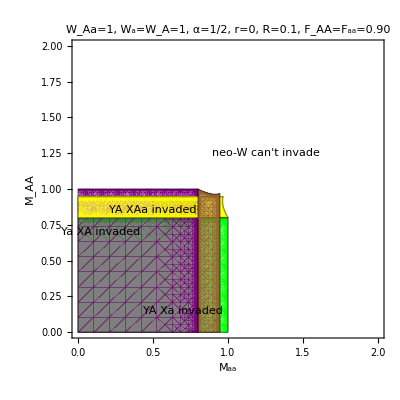

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
Epilog->{
Rotate[Text["YA XAa invaded",{0.5,0.85}],0],
Rotate[Text["Ya XA invaded",{0.15,0.7}],π/2],
Rotate[Text["YA Xa invaded",{0.7,0.15}],0],
Rotate[Text["neo-W can't invade",{1.25,1.25}],0]
},
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0.1, F_AA=F_aa=0.90"
]
```

#### Parameters

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->1.05,
recAMnotAX->0.1
};
YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.someparams,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYaXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.someparams,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYAXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

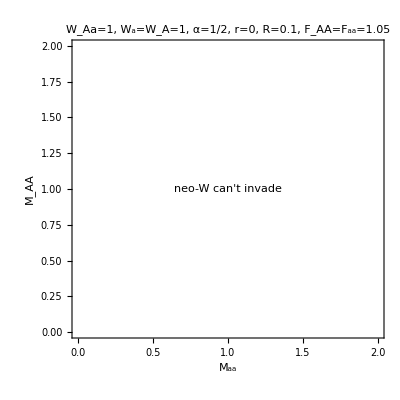

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
Epilog->{
(*Rotate[Text["YA XAa invaded",{0.5,0.9}],0],
Rotate[Text["Ya XA invaded",{0.25,0.5}],π/2],
Rotate[Text["YA Xa invaded",{0.5,0.25}],0],*)
Rotate[Text["neo-W can't invade",{1,1}],0]
},
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0.1, F_AA=F_aa=1.05"
]
```

### Invasion plot (no haploid selection, female homozygotes equivalent, R=0)

#### Parameters

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.60,
recAMnotAX->0
};
YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.someparams,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYaXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.someparams,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYAXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
Epilog->{
Rotate[Text["YA XAa invaded",{0.3,0.9}],0],
Rotate[Text["Ya XA invaded",{0.1,0.35}],π/2],
Rotate[Text["YA Xa invaded",{0.35,0.1}],0],
Rotate[Text["Ya XAa invaded",{1.0,0.2}],0]
},
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=R=0, F_AA=F_aa=0.60"
]
```

-Graphics-

#### Parameters

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.90,
recAMnotAX->0
};
YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.someparams,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYaXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.someparams,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYAXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
Epilog->{
Rotate[Text["YA XAa invaded",{0.5,0.85}],0],
Rotate[Text["Ya XA invaded",{0.15,0.7}],π/2],
Rotate[Text["YA Xa invaded",{0.7,0.15}],0],
Rotate[Text["",{1.25,1.25}],0]
},
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=R=0, F_AA=F_aa=0.90"
]
```

-Graphics-

## MFS vs SPO (r=R=0)

### Set-up

The MFS hypothesis is at work when we have a “perverse” equilibrium and the Y is more associated than the male X with the allele that makes better females.

The SPO hypothesis is at work when the Xs are more associated with the allele that makes better females, but the female X is not as associated with the allele that makes good females as it could be since the X spends some time in males.

We can differentiate between the two hypotheses when r=R=0 by looking at the eigenvalues of W-a and W-A (from turnoverSOM.nb)

```mathematica
{λWa,λWA}={(Subscript[wHap, a,female] ((-1+pAveM) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+2 pAveM (-1+Subscript[α, female]) Subscript[wHap, A,male] Subscript[wDip, a,A,female]))/(2 (-1+freqYm) meanF),(Subscript[wHap, A,female] (2 (-1+pAveM) Subscript[α, female] Subscript[wHap, a,male] Subscript[wDip, A,a,female]-pAveM Subscript[wHap, A,male] Subscript[wDip, A,A,female]))/(2 (-1+freqYm) meanF)}/.meanF->(1-pXf)Subscript[wHap, a,female] (1-pXm)Subscript[wHap, a,male] Subscript[wDip, a,a,female]+pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female]/.pAveM->(1-freqYm)pXm+freqYm pYm//Simplify
```

{-(wHap_(a,female) ((1+(-1+freqYm) pXm-freqYm pYm) wHap_(a,male) wDip_(a,a,female)+2 ((-1+freqYm) pXm-freqYm pYm) (-1+α_female) wHap_(A,male) wDip_(a,A,female)))/(2 (-1+freqYm) ((-1+pXf) wHap_(a,female) ((-1+pXm) wHap_(a,male) wDip_(a,a,female)-pXm wHap_(A,male) wDip_(a,A,female))+pXf wHap_(A,female) (-(-1+pXm) wHap_(a,male) wDip_(A,a,female)+pXm wHap_(A,male) wDip_(A,A,female)))),-(wHap_(A,female) (2 (1+(-1+freqYm) pXm-freqYm pYm) α_female wHap_(a,male) wDip_(A,a,female)+(pXm-freqYm pXm+freqYm pYm) wHap_(A,male) wDip_(A,A,female)))/(2 (-1+freqYm) ((-1+pXf) wHap_(a,female) ((-1+pXm) wHap_(a,male) wDip_(a,a,female)-pXm wHap_(A,male) wDip_(a,A,female))+pXf wHap_(A,female) (-(-1+pXm) wHap_(a,male) wDip_(A,a,female)+pXm wHap_(A,male) wDip_(A,A,female))))}

When the W with the allele not on the Y spreads, we have the SPO hypothesis, while when the W with the allele on the Y spreads, we have the MFS hypothesis.

### No haploid selection, no sex differences (Otto 2014, Fig 3)

#### Parameters

```mathematica
params={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,sex_]->Subscript[wDip, a,a],Subscript[wDip, A,A,sex_]->Subscript[wDip, A,A]
};

Simplify[charpolyYaXAar0/.params,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;

Simplify[charpolyYAXAar0/.params,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;

(*SPO*)
plot1=RegionPlot[
Max[Abs[intYaXAar0]]<1&&(*internally stable*)
λWA>1/.eqr0YaXAa/.params,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot2=RegionPlot[
Max[Abs[intYAXAar0]]<1&&(*internally stable*)
λWa>1/.eqr0YAXAa/.params,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Orange,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot3=RegionPlot[
Max[Abs[intYAXAar0]]<1&&(*internally stable*)
λWA>1/.eqr0YAXAa/.params,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot4=RegionPlot[
Max[Abs[intYaXAar0]]<1&&(*internally stable*)
λWa>1/.eqr0YaXAa/.params,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot5=RegionPlot[
Max[Abs[λ/.YAXaEigs/.params//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YAXa/.params,(*MFS*)
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot6=RegionPlot[
Max[Abs[λ/.YaXAEigs/.params//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YaXA/.params,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Cyan,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
plot1,plot2,plot3,plot4,plot5,plot6,
PlotRangePadding->None,
FrameLabel->{Style["W_aa",20],Style["W_AA",20]},
PlotLabel->Style["W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0",16],
FrameTicksStyle->16,
Epilog->{
Rotate[Text[Style["YA-XAa",12],{0.25,0.8}],0],
Rotate[Text[Style["Ya-XAa",12],{0.8,0.25}],0]
}
]
```

-Graphics-

### Invasion plot (no haploid selection, female homozygotes equivalent)

#### Parameters (fig 2a)

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.60,
recAMnotAX->0
};

Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;

Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;

(*SPO*)
plot1=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot2=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Orange,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot3=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot4=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot5=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YAXa/.someparams/.moreparams,(*MFS*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot6=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Cyan,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
plot1,plot2,plot3,plot4,plot5,plot6,
Epilog->{
Rotate[Text["Ya XAa",{1.5,0.75}],0],
Rotate[Text["YA XAa",{0.75,1.5}],0]
},
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0, F_AA=F_aa=0.60"
]
```

-Graphics-

#### Parameters (fig 2a)

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.60,
recAMnotAX->0
};

Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;

Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;

(*SPO*)
plot1=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot2=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot3=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot4=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YAXa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot5=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot6=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot7=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YAXa/.someparams/.moreparams,(*MFS*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot8=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
plot1,plot2,plot3,plot4,plot5,plot6,plot7,plot8,
(*Epilog->{
Rotate[Text[Style["SPO",20],{1.5,1.5}],0],
Rotate[Text[Style["MFS",20],{0.4,0.4}],0]
},*)
PlotRangePadding->None,
FrameLabel->{Style["M_aa",20],Style["M_AA",20]},
PlotLabel->Style["W_Aa=1, W_a=W_A=1, α=1/2, r=R=0, F_AA=F_aa=0.60",12],
FrameTicksStyle->16
]

Export[plotdir<>"regionplot_2a.pdf",%];
```

-Graphics-

#### Parameters (fig 2b)

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.75,
recAMnotAX->0
};

Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;

Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;

(*SPO*)
plot1=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot2=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot3=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot4=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YAXa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot5=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YaXa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot6=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YAXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot7=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot8=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot9=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YAXa/.someparams/.moreparams,(*MFS*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot10=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];
```

#### Parameters (fig 2b) - extended

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.75,
recAMnotAX->0
};

Mmax=4;

Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;

Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;

(*SPO*)
plot1=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot2=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot3=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot4=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YAXa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot5=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YaXa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot6=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YAXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot7=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot8=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot9=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YAXa/.someparams/.moreparams,(*MFS*)
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot10=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
plot1,plot2,plot3,plot4,plot5,plot6,plot7,plot8,plot9,plot10,
(*Epilog->{
Rotate[Text[Style["SPO",20],{1.5,1.5}],0],
Rotate[Text[Style["MFS",20],{0.4,0.4}],0]
},*)
PlotRangePadding->None,
FrameLabel->{Style["M_aa",20],Style["M_AA",20]},
PlotLabel->Style["W_Aa=1, W_a=W_A=1, α=1/2, r=R=0, F_AA=F_aa=0.75",12],
FrameTicksStyle->16
]
```

-Graphics-

#### Parameters

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.75,
recAMnotAX->0.1
};
Mmax=4;

YAXAExtstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Gray,Opacity[0.5]}
];

YaXaExtstabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Gray,Opacity[0.5]}
];

YAXaExtstabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YAXaExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Gray,Opacity[0.5]},
MaxRecursion->10
];

YaXAExtstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
Max[λ/.YaXAExtEigs/.someparams/.moreparams//Flatten]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Gray,Opacity[0.5]},
MaxRecursion->10
];

Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYaXAar0/.someparams,posassumps];
extYaXAar0=λ/.Solve[%==0,λ]//Flatten;

YaXAaExtstabplot=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYaXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Gray,Opacity[0.5]},
MaxRecursion->10
];

Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
Simplify[charpolyExtYAXAar0/.someparams,posassumps];
extYAXAar0=λ/.Solve[%==0,λ]//Flatten;

YAXAaExtstabplot=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
Max[extYAXAar0/.moreparams]>1,(*externally unstable*)
{Subscript[wDip, a,a,male],0,Mmax},{Subscript[wDip, A,A,male],0,Mmax},
PlotStyle->{Gray,Opacity[0.5]},
MaxRecursion->10
];
```

#### Plot

```mathematica
Show[
YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
(*Epilog->{
Rotate[Text["YA XAa invaded",{0.5,0.9}],0],
Rotate[Text["Ya XA invaded",{0.25,0.5}],π/2],
Rotate[Text["YA Xa invaded",{0.5,0.25}],0],
Rotate[Text["Ya XAa invaded",{1,0.5}],0]
},*)
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0.1, F_AA=F_aa=0.75"
]
```

-Graphics-

```mathematica
Show[
plot1,plot2,plot3,plot4,plot5,plot6,plot7,plot8,plot9,plot10,YAXAExtstabplot,YaXaExtstabplot,YAXaExtstabplot,YaXAExtstabplot,YAXAaExtstabplot,YaXAaExtstabplot,
PlotRangePadding->None,
FrameLabel->{"M_aa","M_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0, R=0 or 0.5, F_AA=F_aa=0.75"
]
```

-Graphics-

#### Parameters (fig 2d)

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->1.05,Subscript[wDip, A,A,female]->0.6
};
moreparams={
recAMnotAX->0
};
```

```mathematica
Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;

Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*SPO*)
plot1=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot2=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot3=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*SPO*)
plot4=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YAXa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Red,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot5=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1&&(*internally stable*)
λWA>1/.eqr0YAXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot6=RegionPlot[
Max[Abs[intYaXAar0/.moreparams]]<1&&(*internally stable*)
λWa>1/.eqr0YaXAa/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot7=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWA>1/.eqr0YAXa/.someparams/.moreparams,(*MFS*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];

(*MFS*)
plot8=RegionPlot[
Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1&&(*internally stable*)
λWa>1/.eqr0YaXA/.someparams/.moreparams,
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Blue,Opacity[0.5]},
MaxRecursion->10
];
```

```mathematica
plot3
```

-Graphics-

#### Plot

```mathematica
Show[
plot1,plot2,plot3,plot4,plot5,plot6,plot7,plot8,
(*Epilog->{
Rotate[Text[Style["SPO",20],{1.5,1.5}],0],
Rotate[Text[Style["MFS",20],{0.4,0.4}],0]
},*)
PlotRangePadding->None,
FrameLabel->{Style["M_aa",20],Style["M_AA",20]},
PlotLabel->Style["W_Aa=1, W_a=W_A=1, α=1/2, r=R=0, F_AA=0.60, F_aa=1.05",12],
FrameTicksStyle->16
]
```

-Graphics-

## analytically get gray region

```mathematica
{λWa,λWA}={(Subscript[wHap, a,female] ((-1+pAveM) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+(1-R)2 pAveM (-1+Subscript[α, female]) Subscript[wHap, A,male] Subscript[wDip, a,A,female]))/(2 (-1+freqYm) meanF),(Subscript[wHap, A,female] ((1-R)2 (-1+pAveM) Subscript[α, female] Subscript[wHap, a,male] Subscript[wDip, A,a,female]-pAveM Subscript[wHap, A,male] Subscript[wDip, A,A,female]))/(2 (-1+freqYm) meanF)};
```

```mathematica
{ρWa,ρWA}={(R pAveM Subscript[wHap, A,male] (1-Subscript[α, female]) Subscript[wHap, a,female] Subscript[wDip, A,a,female])/((1-freqYm)meanF),(R (1-pAveM) Subscript[wHap, a,male] Subscript[α, female] Subscript[wHap, A,female] Subscript[wDip, a,A,female])/((1-freqYm)meanF)};
```

```mathematica
weaksel={
Subscript[wHap, x_,sex_]->1+Subscript[sHap, x,sex] ϵ,
Subscript[wDip, x_,y_,sex_]->1+ Subscript[sDip, x,y,sex] ϵ,
Subscript[α, sex_]->1/2+Subscript[α1, sex] ϵ/2
};
```

```mathematica
charpolyk1=λ^2-(λWA+λWa)λ+(λWA λWa - ρWA ρWa)/.pAveM->pXm(1-freqYm)+freqYm pYm/.meanF->(1-pXf)Subscript[wHap, a,female] (1-pXm)Subscript[wHap, a,male] Subscript[wDip, a,a,female]+pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

```mathematica
weakgenRA=oλ1/.Flatten[Solve[Normal[Series[charpolyk1/.λ->1+oλ1 ϵ/.eqr0YAXAa/.weaksel/.Subscript[sDip, a,A,sex_]->Subscript[sDip, A,a,sex],{ϵ,0,1}]]==0,oλ1]]//Factor
```

((-2 α1_female-α1_male+2 sHap_(a,female)+sHap_(a,male)-2 sHap_(A,female)-sHap_(A,male)+2 sDip_(A,a,female)+sDip_(A,a,male)-2 sDip_(A,A,female)-sDip_(A,A,male)) (6 α1_female-5 α1_male-2 sHap_(a,female)+sHap_(a,male)+2 sHap_(A,female)-sHap_(A,male)+2 sDip_(A,a,female)-3 sDip_(A,a,male)-2 sDip_(A,A,female)+3 sDip_(A,A,male)))/(16 (sDip_(a,a,female)-2 sDip_(A,a,female)+sDip_(A,A,female)))

```mathematica
weakgenRB=oλ1/.Flatten[Solve[Normal[Series[charpolyk1/.λ->1+oλ1 ϵ/.eqr0YAXa/.weaksel/.Subscript[sDip, a,A,sex_]->Subscript[sDip, A,a,sex],{ϵ,0,1}]]==0,oλ1]]//Factor
```

1/4 (4 α1_male-2 sHap_(a,female)-2 sHap_(a,male)+2 sHap_(A,female)+2 sHap_(A,male)-3 sDip_(a,a,female)+2 sDip_(A,a,female)+sDip_(A,A,female))

```mathematica
Normal[Series[(λWA-1) pAveM+(λWa-1)(1-pAveM)/.R->0/.pAveM->pXm(1-freqYm)+freqYm pYm/.meanF->(1-pXf)Subscript[wHap, a,female] (1-pXm)Subscript[wHap, a,male] Subscript[wDip, a,a,female]+pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female]/.eqr0YAXa/.weaksel/.Subscript[sDip, a,A,sex_]->Subscript[sDip, A,a,sex],{ϵ,0,1}]]-weakgenRB/.ϵ->1//Factor
```

0

```mathematica
Normal[Series[(λWA-1) pAveM+(λWa-1)(1-pAveM)/.R->0/.pAveM->pXm(1-freqYm)+freqYm pYm/.meanF->(1-pXf)Subscript[wHap, a,female] (1-pXm)Subscript[wHap, a,male] Subscript[wDip, a,a,female]+pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female]/.eqr0YAXAa/.weaksel/.Subscript[sDip, a,A,sex_]->Subscript[sDip, A,a,sex],{ϵ,0,1}]]-weakgenRA/.ϵ->1//Factor
```

0

```mathematica
params={Subscript[α1, sex_]->0,Subscript[sHap, x_,sex_]->0,Subscript[sDip, A,a,sex_]->0,Subscript[sDip, a,A,sex_]->0,Subscript[sDip, a,a,female]->-0.25,Subscript[sDip, A,A,female]->-0.25};
```

```mathematica
Solve[0==weakgenRA,Subscript[sDip, A,A,male]]
%/.params
```

{{sDip_(A,A,male)→-2 α1_female-α1_male+2 sHap_(a,female)+sHap_(a,male)-2 sHap_(A,female)-sHap_(A,male)+2 sDip_(A,a,female)+sDip_(A,a,male)-2 sDip_(A,A,female)},{sDip_(A,A,male)→1/3 (-6 α1_female+5 α1_male+2 sHap_(a,female)-sHap_(a,male)-2 sHap_(A,female)+sHap_(A,male)-2 sDip_(A,a,female)+3 sDip_(A,a,male)+2 sDip_(A,A,female))}}

{{sDip_(A,A,male)→0.5},{sDip_(A,A,male)→-0.166667}}

```mathematica
Plot[weakgenRA/.params/.Subscript[sDip, A,A,male]->Subscript[wDip, A,A,male]-1,{Subscript[wDip, A,A,male],0,2}]
```

-Graphics-

```mathematica
someparams={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,female]->Subscript[wDip, homo,female],Subscript[wDip, A,A,female]->Subscript[wDip, homo,female]
};
moreparams={
Subscript[wDip, homo,female]->0.75,
recAMnotAX->1/2
};
```

```mathematica
Simplify[charpolyYAXAar0/.someparams,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
```

```mathematica
intstabplotYAXAar0=RegionPlot[
Max[Abs[intYAXAar0/.moreparams]]<1,(*internally stable*)
{Subscript[wDip, a,a,male],0,2},{Subscript[wDip, A,A,male],0,2},
PlotStyle->{Orange,Opacity[0.5]},
MaxRecursion->10
];
```

```mathematica
Show[
RegionPlot[0<weakgenRA/.params/.Subscript[sDip, x_,y_,male]->Subscript[wDip, x,y,male]-1,{ Subscript[wDip, a,a,male],0,4},{ Subscript[wDip, A,A,male],0,4}],
intstabplotYAXAar0,
YAXAaExtstabplot
]
```

-Graphics-

```mathematica
intstabplotYAXar0=RegionPlot[
Max[Abs[λ/.YAXaEigs/.someparams/.moreparams//Flatten]]<1,(*internally stable*)
{Subscript[wDip, a,a,male],0,4},{Subscript[wDip, A,A,male],0,4},
PlotStyle->{Orange,Opacity[0.5]},
MaxRecursion->10
];
```

```mathematica
Show[
RegionPlot[0<weakgenRB/.params/.Subscript[sDip, x_,y_,male]->Subscript[wDip, x,y,male]-1,{ Subscript[wDip, a,a,male],0,4},{ Subscript[wDip, A,A,male],0,4}],
intstabplotYAXar0,
YAXaExtstabplot
]
```

-Graphics-